```mathematica
ClearAll["Global`*"]
```

```mathematica
t3=Import["/Users/michelecastellana/Documents/finite_elements/dynamics/channel_with_cylinder_flat_cn/solution_3/data.csv"]
```

```mathematica
t3=Table[{t3[[i,1]],Log[Abs[t3[[i,4]]]]/Log[10]},{i,2,Length[t3]}]
```

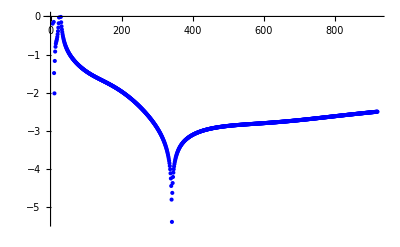

```mathematica
ListPlot[t3,PlotStyle->Blue]
```